U=-G M((2 r_0)/r+1/(2 r^3))

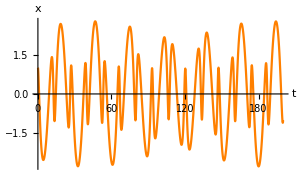
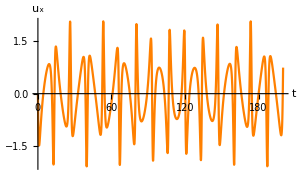
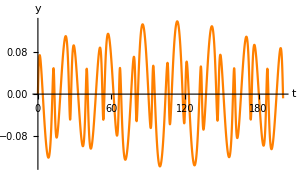
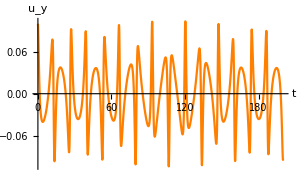
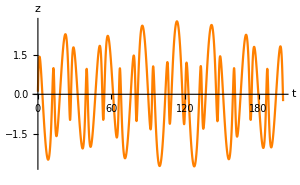
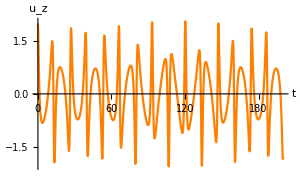
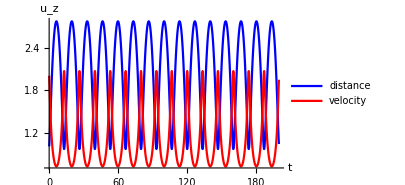
Energy: -0.487593
Angular momentum: {-0.01,-2.,0.1} -> 2.00252

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics3D-

```mathematica
ClearAll["Global`*"]
(* r(t) *)
r=√(x[t]^2+y[t]^2+z[t]^2);
(* Potential *)
U=-G M((2Norm[r0])/r+1/(2 r^3));
(* Differential equations *)
deq={x''[t]==-D[U,x[t]], y''[t]==-D[U,y[t]], z''[t]==-D[U,z[t]]};
(* Initial conditions *)
InitialConditions={x[0]==x0, y[0]==y0, z[0]==z0, x'[0]==vx0, y'[0]==vy0, z'[0]==vz0};
IVP=Join[deq,InitialConditions];
r0={x0,y0,z0};
v0={vx0,vy0,vz0};
G=1;M=1;
x0=1; y0=0; z0=0.1;
vx0=0; vy0=0.1; vz0=2.0;
(* Integrals *)
Energy=1/2 M v0.v0+U/.{x[t]->x0, y[t]->y0, z[t]->z0};
AngularMomentum=Cross[r0,v0] ;
(* numerical solution *)
tmax=200;
sol=NDSolve[IVP,{x[t],y[t],z[t]},{t,0,tmax},Method->Automatic];
xt=x[t]/.sol[[1]];
yt=y[t]/.sol[[1]];
zt=z[t]/.sol[[1]];
vxt=D[x[t]/.sol[[1]],t];
vyt=D[y[t]/.sol[[1]],t];
vzt=D[z[t]/.sol[[1]],t];
(* distance & velocity *)
rt=Sqrt[xt^2+yt^2+zt^2];
vt=Sqrt[vxt^2+vyt^2+vzt^2];
(* presentation *)
Column[{
StringForm["Energy: ``",Energy],
StringForm["Angular momentum: `` -> ``",AngularMomentum, Norm[AngularMomentum]],
"",
Row[{
Plot[xt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","x"},PlotStyle->Orange],
Plot[vxt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","u_x"},PlotStyle->Orange]
}],
Row[{
Plot[yt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","y"},PlotStyle->Orange],
Plot[vyt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","u_y"},PlotStyle->Orange]
}],
Row[{
Plot[zt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","z"},PlotStyle->Orange],
Plot[vzt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","u_z"},PlotStyle->Orange]
}],
Plot[{rt,vt},{t,0,tmax},ImageSize->300,AxesLabel->{"t","u_z"},PlotStyle->{Blue,Red},PlotLegends->LineLegend[{Blue,Red},{"distance","velocity"}]],
ParametricPlot3D[{xt,yt,zt},{t,0,tmax},ImageSize->Large,PlotTheme->"Scientific",
Epilog->{PointSize[0.05],Point[{0,0,0}]}];
Show[
ParametricPlot3D[{xt,yt,zt},{t,0,tmax},ImageSize->Large,PlotTheme->"Scientific",ColorFunction->"Rainbow"],
Graphics3D[{PointSize[0.04],Point[{0,0,0}]}],
PlotRange->{{-4,4},{-4,4},{-4,4}}
]
},Alignment->Center]
```

Το σύστημα για κάποιες τιμές αρχικών συνθηκών κινείται ανάμεσα σε δύο οριακούς κύκλους, επομένως έχει σταθερές τροχιές.

U=-G M((2 r_0)/r^4+1/(2 r^2))

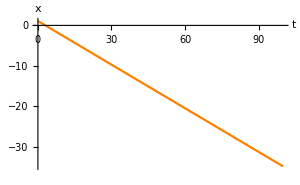
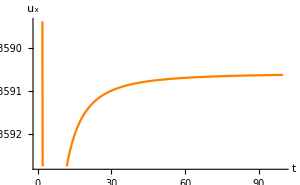
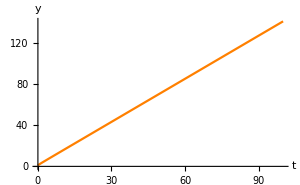
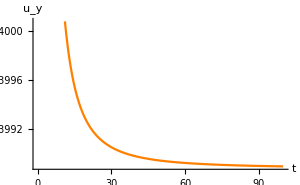
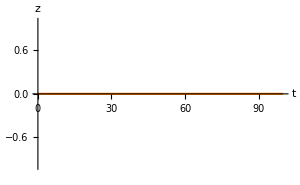
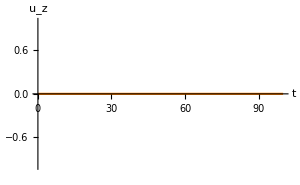
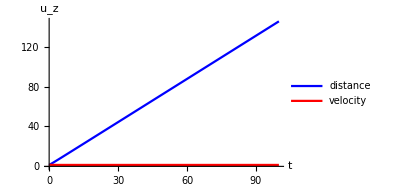
Energy: 1.04289
Angular momentum: {0.,0.,2.} -> 2.

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics3D-

```mathematica
ClearAll["Global`*"]
(* r(t) *)
r=√(x[t]^2+y[t]^2+z[t]^2);
(* Potential *)
U=-G M((2Norm[r0])/r^4+1/(2 r^2));
(* Differential equations *)
deq={x''[t]==-D[U,x[t]], y''[t]==-D[U,y[t]], z''[t]==-D[U,z[t]]};
(* Initial conditions *)
InitialConditions={x[0]==x0, y[0]==y0, z[0]==z0, x'[0]==vx0, y'[0]==vy0, z'[0]==vz0};
IVP=Join[deq,InitialConditions];
r0={x0,y0,z0};
v0={vx0,vy0,vz0};
G=1;M=1;
x0=1.0; y0=1.0; z0=0;
vx0=0.0; vy0=2.0; vz0=0.0;
(* Integrals *)
Energy=1/2 M v0.v0+U/.{x[t]->x0, y[t]->y0, z[t]->z0};
AngularMomentum=Cross[r0,v0] ;
(* numerical solution *)
tmax=100;
sol=NDSolve[IVP,{x[t],y[t],z[t]},{t,0,tmax},Method->Automatic];
xt=x[t]/.sol[[1]];
yt=y[t]/.sol[[1]];
zt=z[t]/.sol[[1]];
vxt=D[x[t]/.sol[[1]],t];
vyt=D[y[t]/.sol[[1]],t];
vzt=D[z[t]/.sol[[1]],t];
(* distance & velocity *)
rt=Sqrt[xt^2+yt^2+zt^2];
vt=Sqrt[vxt^2+vyt^2+vzt^2];
(* presentation *)
Column[{
StringForm["Energy: ``",Energy],
StringForm["Angular momentum: `` -> ``",AngularMomentum, Norm[AngularMomentum]],
"",
Row[{
Plot[xt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","x"},PlotStyle->Orange],
Plot[vxt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","u_x"},PlotStyle->Orange]
}],
Row[{
Plot[yt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","y"},PlotStyle->Orange],
Plot[vyt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","u_y"},PlotStyle->Orange]
}],
Row[{
Plot[zt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","z"},PlotStyle->Orange],
Plot[vzt,{t,0,tmax},ImageSize->300,AxesLabel->{"t","u_z"},PlotStyle->Orange]
}],
Plot[{rt,vt},{t,0,tmax},ImageSize->300,AxesLabel->{"t","u_z"},PlotStyle->{Blue,Red},PlotLegends->LineLegend[{Blue,Red},{"distance","velocity"}]],
ParametricPlot3D[{xt,yt,zt},{t,0,tmax},ImageSize->Large,PlotTheme->"Scientific",
Epilog->{PointSize[0.05],Point[{0,0,0}]}];
Show[
ParametricPlot3D[{xt,yt,zt},{t,0,tmax},ImageSize->Large,PlotTheme->"Scientific",ColorFunction->"Rainbow"],
Graphics3D[{PointSize[0.04],Point[{0,0,0}]}],
PlotRange->{{-4,4},{-4,4},{-4,4}}
]
},Alignment->Center]
```

Κάνοντας δοκιμές μόνο δεν μπόρεσα να βρω κλειστές τροχιές για αυτό το δυναμικό (δεν το έψαξα διεξοδικά, και δεν έκανα και ανάλυση στο χαρτί για να δω αν όντως υπάρχουν ή όχι - από τη μορφή του δυναμικού φαίνεται ότι θα πρέπει να υπάρχουν).